# Lab 2 - Truncation Errors

## Kyle Perra 6/25/2015

## Sine Degree Calculations

```mathematica
sin[704 Degree]
```

sin[704 °]

```mathematica
N[Sin[704 Degree]]
```

-0.275637

```mathematica
SetPrecision[N[Sin[704 Degree]], 30]
```

-0.275637355816999163327096766807

## Sine Radian Calculations

```mathematica
Sin[12.3]
```

-0.263232

```mathematica
SetPrecision[Sin[12.3],20]
```

-0.26323179136580093784

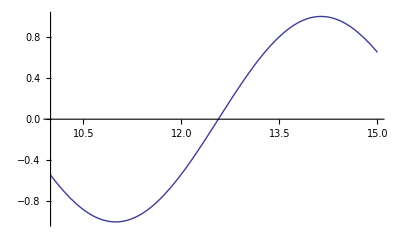

```mathematica
Plot[Sin[x], {x,10,15}]
```

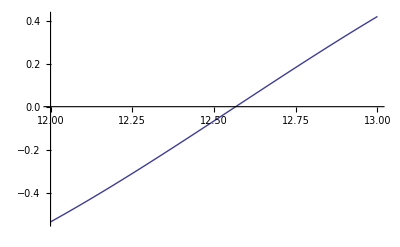

```mathematica
Plot[Sin[x],{x,12,13}]
```

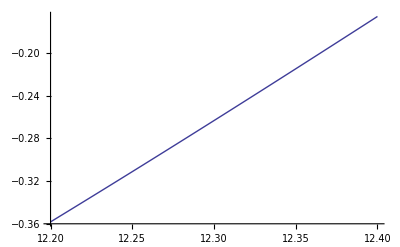

```mathematica
Plot[Sin[x],{x,12.2,12.4}]
```

## Maclaurin Expansion of Sin(x)

```mathematica
valX = 12.3;
result = 0;
numTerms = 26;
```

```mathematica
Do[Print[result = result + ((-1)^(i-1))*(valX^(2*i-1))/Factorial[2*i-1]],{i,numTerms}]
```

12.3

-297.845

2048.24

-6402.7

11354.8

-13068.2

10617.5

-6446.39

3044.75

-1153.84

358.553

-93.6388

20.3815

-4.19133

0.387027

-0.357767

-0.251063

-0.264629

-0.263088

-0.263245

-0.263231

-0.263232

-0.263232

-0.263232

«2 more identical outputs»

```mathematica
SetPrecision[result,10]
```

-0.2632317914